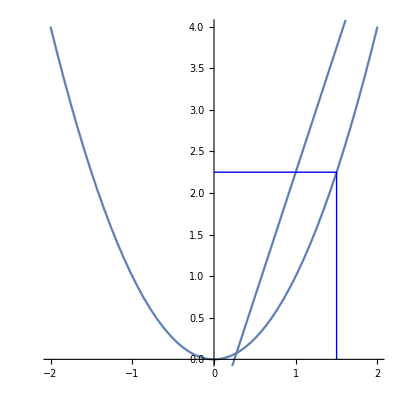

```mathematica
Corner[Subscript[x_, 0]]:=Line[{{Subscript[x, 0],0},{Subscript[x, 0],Subscript[x, 0]^2},{0,Subscript[x, 0]^2}}];

Show[
Plot[x^2, {x, -2, 2}],
Plot[2 1.5 x+(1.5^2-2 1.5), {x, -2, 2}],
Graphics[{ Thin,Blue,
Corner[1.5]

}],
AspectRatio->1,
PlotRange->{{-2,2},{0,4}}
]
```

```mathematica
f[x_]:=x^2
x0=1.5
```

```mathematica
d[x_]:=f'[x0]x-x0^2
```